Partition Function For a Freely Jointed Chain 1D
Hemant Tailor

## 1-D Model Constituents of the Final Partiton Function & Constants

```mathematica
a=1;
p=0.1;

Const[n_] =1/(2Factorial[n-1])(1/(2 p))^n;

η[n_,k1_,k2_,R_]:= a (n - 2k1) + p/2 (n -2k2) -R;
DoubleBinomial[n_,k1_,k2_]:= Binomial[n,k1] Binomial[n,k2];

F[n_,k1_,k2_]:= a(n -2 k1) + p/2(n-2k2);
TopHat[n_,k1_,k2_,R_]:=UnitStep[R-F[n,k1,n]]UnitStep[F[n,k1,0]-R];

InternalSumFuntion[n_,k1_,k2_,R_]:= (-1)^k2 DoubleBinomial[n,k1,k2] η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]
InternalSumFuntionModified[n_,k1_,k2_,R_]:=(-1)^k2 DoubleBinomial[n,k1,k2] η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]TopHat[n,k1,k2,R]
```

Parition Function Equations Z(R):

```mathematica
PartitionFunction[n_,R_] :=Const[n]Sum[InternalSumFuntion[n,k1,k2,R],{k1,0,n},{k2,0,n}]
PartitionFunctionModified[n_,R_] :=Const[n]Sum[InternalSumFuntionModified[n,k1,k2,R],{k1,0,n},{k2,0,n}]
```

## Results for Z(0)

Results for Z(0) against N

{{2,5.},{4,2.5},{6,1.71875},{8,1.31077},{10,1.06249}}

{{2,5.},{4,2.5},{6,1.71875},{8,1.31076},{10,1.05923},{12,0.888641},{14,0.765352},{16,0.672094},{18,0.599087},{20,0.540384}}

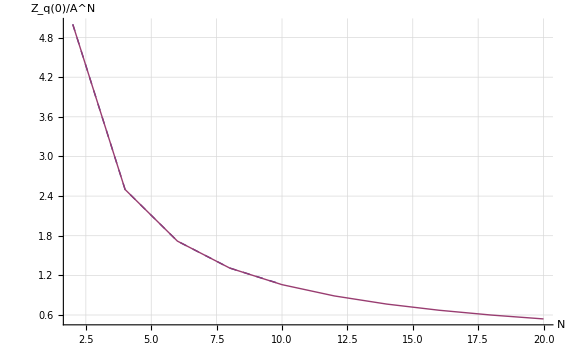

```mathematica
R0Data=Table[{n,PartitionFunction[n,0]},{n,2,10,2}]
R0ModifiedData=Table[{n,PartitionFunctionModified[n,0]},{n,2,20,2}]
ListLinePlot[{R0Data,R0ModifiedData},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{{Thick,Dashed},Thick},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Large,LabelStyle->{"Times",16},AxesLabel->{Style["N",FontSize->18],Style["Z_q(0)/A^N",FontSize->18]}]
```

## Results

Results for Z for given N (The partition functions contains the top hat fuction)

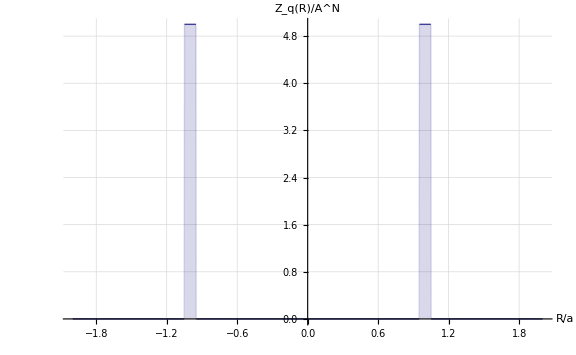
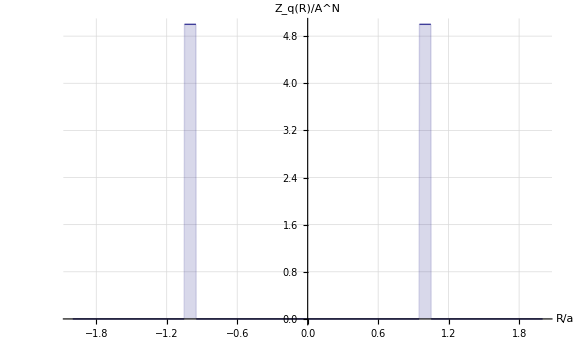

```mathematica
nx=1;
{Plot[PartitionFunction[nx,R],{R,-nx-1,nx+1},PlotRange->All,Filling->Bottom,PlotStyle->Thick,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Large,LabelStyle->{16},AxesLabel->{Style["R/a",FontSize->18],Style["Z_q(R)/A^N",FontSize->18]}],Plot[PartitionFunctionModified[nx,R],{R,-nx-1,nx+1},PlotRange->All,Filling->Bottom,PlotStyle->Thick,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Large,LabelStyle->{16},AxesLabel->{Style["R/a",FontSize->18],Style["Z_q(R)/A^N",FontSize->18]}]}
```

Results for Z for given N = 2,4,6,8,10

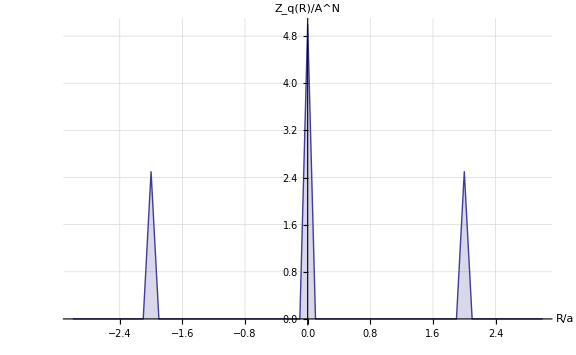
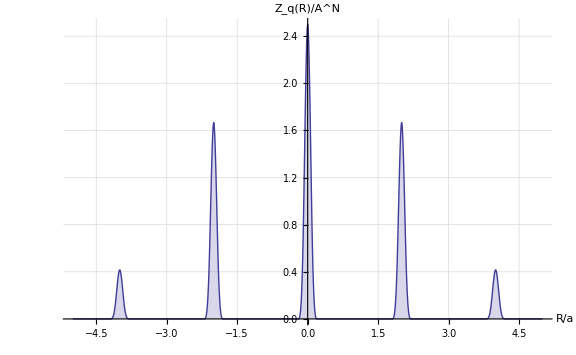
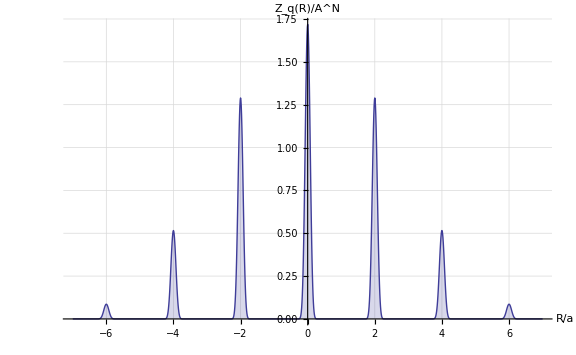
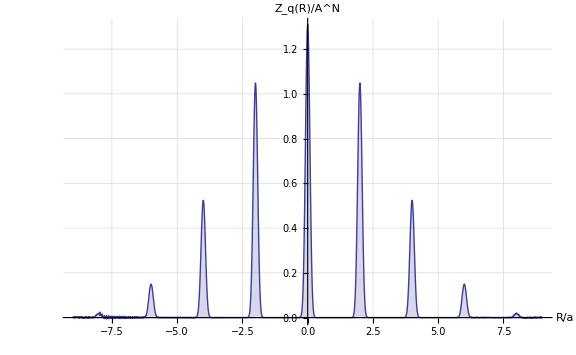
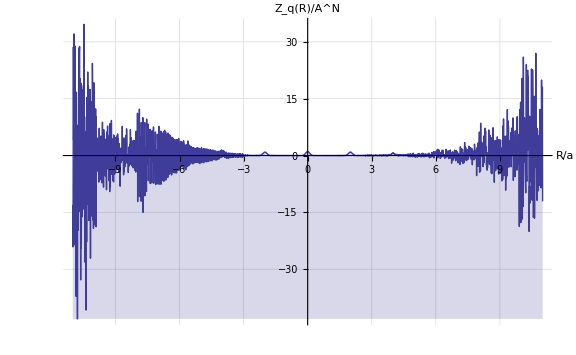

```mathematica
Table[ListLinePlot[Table[{r,PartitionFunction[nx,r]},{r,-nx-1,nx+1,0.01}],PlotRange->All,Filling->Bottom,PlotStyle->Thick,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Large,LabelStyle->{16},AxesLabel->{Style["R/a",FontSize->18],Style["Z_q(R)/A^N",FontSize->18]}],{nx,2,10,2}]
```

From Prof Harkers Notebook

```mathematica
Z[R_,N_,p_,a_]:=1/(2^(N+1) p^N)∑_(k=0)^N ∑_(kp=0)^N (N!)/(k! (N-k)!)(N!)/(kp! (N-kp)!)(-1)^kp(a(N-2k) + p/2(N-2kp)-R)^(N-1)/((N-1)!)Sign[(a(N-2k) + p/2(N-2kp)-R)]
```

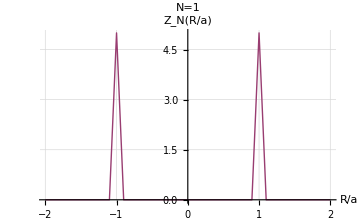
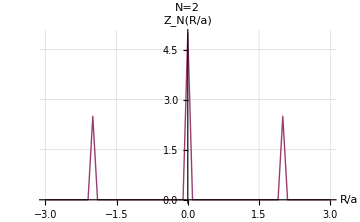
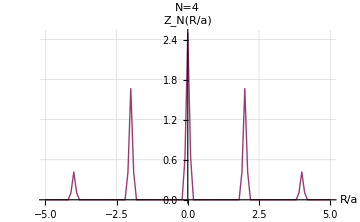
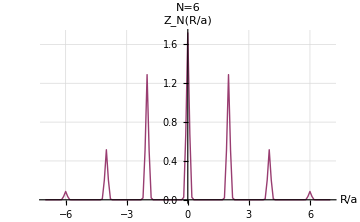
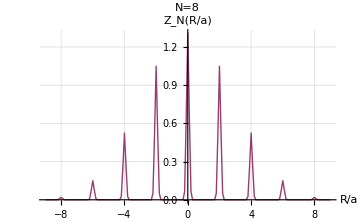
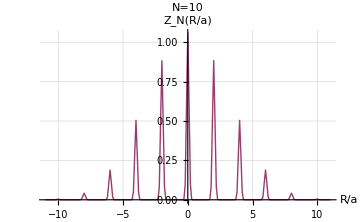
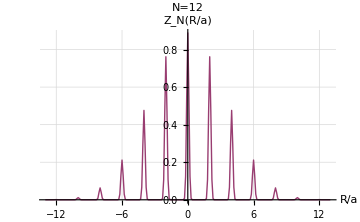
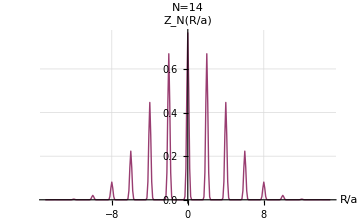

```mathematica
{ListPlot[Table[{R,Z[R,1,1/10,1]},{R,-2,2,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=1"],
ListPlot[Table[{R,Z[R,2,1/10,1]},{R,-3,3,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=2"],
ListPlot[Table[{R,Z[R,4,1/10,1]},{R,-5,5,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=4"],
ListPlot[Table[{R,Z[R,6,1/10,1]},{R,-7,7,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=6"],
ListPlot[Table[{R,Z[R,8,1/10,1]},{R,-9,9,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=8"],
ListPlot[Table[{R,Z[R,10,1/10,1]},{R,-11,11,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=10"],
ListPlot[Table[{R,Z[R,12,1/10,1]},{R,-13,13,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=12"],
ListPlot[Table[{R,Z[R,14,1/10,1]},{R,-15,15,1/10}],Joined->True,PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,ColorData[1,2]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Medium,AxesLabel->{"R/a","Z_N(R/a)"},PlotLabel->"N=14"]}
```

Partition Funtion with R=0

```mathematica
Z0[N_,p_,a_]:=1/(2^(N+1) p^N)∑_(k=0)^N ∑_(kp=0)^N (N!)/(k! (N-k)!)(N!)/(kp! (N-kp)!)(-1)^kp(a(N-2k) + p/2(N-2kp))^(N-1)/((N-1)!)Sign[(a(N-2k) + p/2(N-2kp))]
```

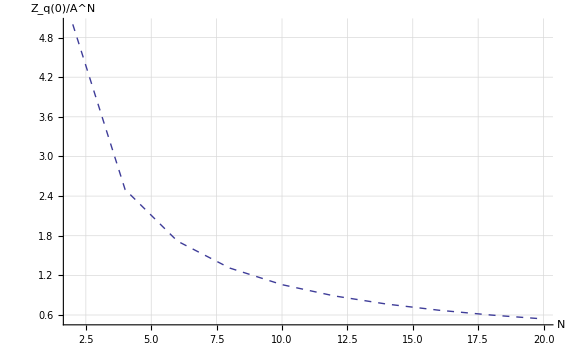

```mathematica
ListLinePlot[Table[{x,Z0[x,1/10,1]},{x,2,20,2}],PlotRange->All,AxesOrigin->{0,0},PlotStyle->{{Thick,Dashed},Thick},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],ImageSize->Large,LabelStyle->{"Times",16},AxesLabel->{Style["N",FontSize->18],Style["Z_q(0)/A^N",FontSize->18]}]
```

## Furthur Analysis

```mathematica
Kernal[n_,k1_,k2_,R_]:= η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]
KernalModified[n_,k1_,k2_,R_]:=  η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]TopHat[n,k1,k2,R]

Kernal2[n_,k1_,k2_,R_]:=(-1)^k2 DoubleBinomial[n,k1,k2] η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]
Kernal3[n_,k1_,k2_,R_]:=(-1)^k2 DoubleBinomial[n,k1,k2] η[n,k1,k2,R]^(n-1)Sign[η[n,k1,k2,R]]TopHat[n,k1,k2,R]
```

```mathematica
nx=2;
rRange=Table[i,{i,-nx,nx,1}]
```

{-2,-1,0,1,2}

```mathematica
DataKernal=Table[
{rRange[[r]],
KernalData=Flatten[Table[Kernal[nx,k1,k2,rRange[[r]]],{k1,0,nx},{k2,0,nx}]],
Total[KernalData],
KernalData2=Flatten[Table[Kernal2[nx,k1,k2,rRange[[r]]],{k1,0,nx},{k2,0,nx}]],
Total[KernalData2]
}
,{r,1,Length[rRange]}
];
Text@Grid[Prepend[DataKernal,{"R","η^(n - 1)sgn[η]_(k, k')","∑_(k, k') η^(n - 1)sgn[η]","(-1)^k2(n,k1,k2)η^(n - 1)sgn[η]","∑_(k, k') (-1)^k2(n,k1,k2)η^(n - 1)sgn[η]"}],Spacings->{Automatic,2},Frame->All]
```

R | η^(n - 1)sgn[η]_(k, k') | ∑_(k, k') η^(n - 1)sgn[η] | (-1)^k2(n,k1,k2)η^(n - 1)sgn[η] | ∑_(k, k') (-1)^k2(n,k1,k2)η^(n - 1)sgn[η]
-2 | {4.1,4.,3.9,2.1,2.,1.9,0.1,0.,0.1} | 18.2 | {4.1,-8.,3.9,4.2,-8.,3.8,0.1,0.,0.1} | 0.2
-1 | {3.1,3.,2.9,1.1,1.,0.9,0.9,1.,1.1} | 15. | {3.1,-6.,2.9,2.2,-4.,1.8,0.9,-2.,1.1} | 4.44089×10^-16
0 | {2.1,2.,1.9,0.1,0.,0.1,1.9,2.,2.1} | 12.2 | {2.1,-4.,1.9,0.2,0.,0.2,1.9,-4.,2.1} | 0.4
1 | {1.1,1.,0.9,0.9,1.,1.1,2.9,3.,3.1} | 15. | {1.1,-2.,0.9,1.8,-4.,2.2,2.9,-6.,3.1} | -4.44089×10^-16
2 | {0.1,0.,0.1,1.9,2.,2.1,3.9,4.,4.1} | 18.2 | {0.1,0.,0.1,3.8,-8.,4.2,3.9,-8.,4.1} | 0.2

```mathematica
DataKernalModified=Table[
{rRange[[r]],
KernalModifiedData=Flatten[Table[KernalModified[nx,k1,k2,rRange[[r]]],{k1,0,nx},{k2,0,nx}]],
Total[KernalModifiedData],
KernalData3=Flatten[Table[Kernal3[nx,k1,k2,rRange[[r]]],{k1,0,nx},{k2,0,nx}]],
Total[KernalData3]
}
,{r,1,Length[rRange]}
];
Text@Grid[Prepend[DataKernalModified,{"R","η^(n - 1)sgn[η]","∑_(k, k') η^(n - 1)sgn[η]","(-1)^k2(n,k1,k2)η^(n - 1)sgn[η]Θ","∑_(k, k') (-1)^k2(n,k1,k2)η^(n - 1)sgn[η]Θ"}],Spacings->{Automatic,2},Frame->All]
```

R | η^(n - 1)sgn[η] | ∑_(k, k') η^(n - 1)sgn[η] | (-1)^k2(n,k1,k2)η^(n - 1)sgn[η]Θ | ∑_(k, k') (-1)^k2(n,k1,k2)η^(n - 1)sgn[η]Θ
-2 | {0.,0.,0.,0.,0.,0.,0.1,0.,0.1} | 0.2 | {0.,0.,0.,0.,0.,0.,0.1,0.,0.1} | 0.2
-1 | {0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0. | {0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0.
0 | {0.,0.,0.,0.1,0.,0.1,0.,0.,0.} | 0.2 | {0.,0.,0.,0.2,0.,0.2,0.,0.,0.} | 0.4
1 | {0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0. | {0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0.
2 | {0.1,0.,0.1,0.,0.,0.,0.,0.,0.} | 0.2 | {0.1,0.,0.1,0.,0.,0.,0.,0.,0.} | 0.2